```mathematica
triangle={{0,1},{-1,-1},{1.5,-1}};
frames=70;
```

```mathematica
index[n_Integer] := Module[{r,i,j=0},
r = Range[n];
For[i=4,i≤n,j=Mod[++i,4],If[j<2 && n>i-j+1,r[[i]]=0]];
DeleteCases[r,0]];
```

```mathematica
p = ConstantArray[Graphics[],frames];
p[[1]]=Graphics@GraphicsComplex[triangle,Point[Range@3]];
p[[2]]=ListPlot[Table[Labeled[triangle[[i]],Text[i],Bottom],{i,3}],
Axes->False,PlotStyle->{Darker@Green,PointSize@Large}];
point=RandomReal/@{{-1.1,.1},{-1,1}};
Do[
j=RandomChoice@Range[3];
middle=Mean@{point,triangle[[j]]};
p[[i + 0]]=Graphics@{PointSize[Medium],Red,Point[point]};
p[[i + 1]]=Graphics@Text[Style[j,Magenta,FontSize->36],{1.4,.9}];
p[[i + 2]]=Graphics@{Blue,Dashed,Line@{point,triangle[[j]]}};
p[[i + 3]]=Graphics@{LightRed,Thin,Line@{point,middle}};
point = middle,
{i,3,frames,4}];
```

```mathematica
Animate[With[{r=index[n]},Show[p[[r]],ImageSize->Large]],
{n,2,frames,1},AnimationRunning->False,
AnimationRepetitions->1,AnimationRate->.7]
```

```mathematica
walk[n_]:=With[{r=index[n]},Show[p[[r]],ImageSize->Large]];
Export["walk.gif",Table[walk[n],{n,2,frames}]]
```

walk.gif

```mathematica
gif=Import["https://i.stack.imgur.com/KRiRX.gif"];
```

#### Implementation of the Chaos Game

```mathematica
start = RandomReal/@{{-1.1, .1}, {-1, 1}};
game[steps_Integer] := Module[{a, c, i, m, p1, p2, p3},
a = ConstantArray[start,steps];
For[i = 1,i <steps,i++,
c = RandomChoice@Range[3];
a[[i + 1]] = (a[[i]] + triangle[[c]])/2];
p1=Graphics@{PointSize[Large],Darker@Green,Point[triangle]};
p2=Graphics@Text[Style["steps" steps,Blue,FontSize->20],{1.2,.9}];
p3=Graphics@{Red,Point[a]};
Show[{p1, p2, p3},ImageSize->Large]]
```

```mathematica
game[500]
```

-Graphics-

#### Sierpiński carpet

```mathematica
pointset=With[{verts=DeleteCases[Tuples[{-1,0,1},{2}],{0,0}],n=10^5},
NestList[(2 RandomChoice[verts]+#)/3 &,RandomReal[{-1,1},2], n]];
```

```mathematica
carpet[n_Integer] := Module[{p0, p1, p2},
p0 = Graphics@{White, Point@Tuples[{-1, 0, 1},{2}]};
p1 = Graphics@{AbsolutePointSize[1/2],Blue,Point@pointset[[1;;n]]};
p2 = Graphics@Text[Style["steps" n, Darker@Green,FontSize -> 18],{0,0}];
Show[{p0, p1, p2}, ImageSize -> Large]]
```

```mathematica
carpet[50000]
```

-Graphics-

#### Pentagonal Snowflake

```mathematica
flake5=With[{verts =Table[{Cos[2 π t/5],Sin[2 π t/5]},{t, 5}],n =10^5},
NestList[(RandomChoice[verts] + #)/(1 + GoldenRatio)&,RandomReal[{-1,1},2],n]];
```

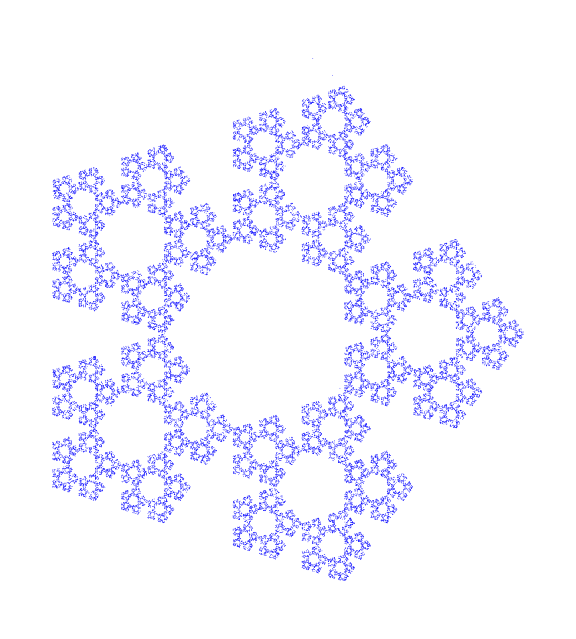

```mathematica
Show[Graphics@{AbsolutePointSize[1/2],Blue,Point@flake5[[1;;50000]]},
ImageSize -> Large]
```

#### Hexagonal Snowflake

```mathematica
flake6=With[{verts =Table[{Cos[2 π t/6],Sin[2 π t/6]},{t,6}],n =10^5},
NestList[(RandomChoice[verts] + #)/3&,RandomReal[{-1,1},2],n]];
```

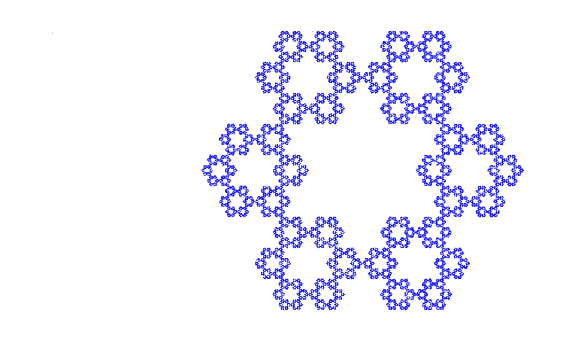

```mathematica
Show[Graphics@{AbsolutePointSize[1/2],Blue,Point@flake6[[1;;50000]]},
ImageSize -> Large]
```